```mathematica
(* If your tagtime gap is g minutes then the probability of at least one ping in any x minute window is 1-exp(-x/g). The window corresponding to probability p is -g*ln(1-p). 
For example, with g=45,there's a 10% chance of getting pinged in any window
of duration 4:44.47.
There's a 50% chance of getting pinged within 31:11.50.
There's a 99% chance of a ping within 3:27:14.
The probability of waiting 10 hours and 22 minutes for a ping is one in a million. *)
```

```mathematica
(* The sum of n exponential random variables, each with rate parameter a, has gamma distribution with shape parameter n and scale parameter 1/a. *)
```

```mathematica
Quit
```

```mathematica
(********************************From mash.pl********************************)ARGV=args=Drop[$CommandLine,4];(*Command line args.*)pr=WriteString["stdout",##]&;(*More*)prn=pr[##,"\n"]&;(*convenient*)perr=WriteString["stderr",##]&;(*print*)perrn=perr[##,"\n"]&;(*statements.*)re=RegularExpression;(*I wish mathematica weren't*)EOF=EndOfFile;(*so damn verbose!*)read[]:=InputString[""];(*Grab a line from stdin.*)readList[]:=Most@(*Grab the list of all the lines*)NestWhileList[read[]&,read[],#=!=EOF&];(*from stdin.*)cat=StringJoin@@(ToString/@{##})&;(*Like sprintf/strout in C/C++.*)eval=ToExpression[cat[##]]&;(*Like eval in every other lang.*)slurp=Import[#,"Text"]&;(*Fetch contents of file as str.*)system=Run@cat@##&;(*System call.*)backtick=Import[cat["!",##],"Text"]&;(*System call;returns stdout.*)(*ABOVE:mma-scripting related.*)keys[f_,i_:1]:=(*BELOW:general utilities.*)DownValues[f,Sort->False][[All,1,1,i]];(*Keys of a hash/dictionary.*)SetAttributes[each,HoldAll];(*each[pattern,list,body]*)each[pat_,lst_List,bod_]:=(*converts pattern to body for*)(Cases[Unevaluated@lst,pat:>bod];Null);(*each element of list.*)each[p_,l_,b_]:=(Cases[l,p:>b];Null);(*(Warning:eats Return[]s.)*)some[f_,l_List]:=True===(*Whether f applied to some*)Scan[If[f[#],Return[True]]&,l];(*element of list is True.*)every[f_,l_List]:=Null===(*Similarly,And@@f/@l*)Scan[If[!f[#],Return[False]]&,l];(*(but with lazy evaluation).*)(******************************************************************************)
```

```mathematica
(* Mostly an alias for AbsoluteTime,but slightly more robust.Also defaults to noon instead of midnight becuase of this:http://stackoverflow.com/q/5794401 *)
tm[]:=AbsoluteTime[]
tm[y_,m_,d_Integer,h_:12,mn_:0,s_:0]:=AbsoluteTime[{y,m,d,h,mn,s}]
tm[y_,m_,d_]:=AbsoluteTime[{y,m,d}] (*allows fractional days*)
tm[d_List]:=tm@@d
tm[d_String]:=Check[AbsoluteTime[d],prn["ERRORtm: ",d,"\n"];Exit[1]]
tm[d_]:=d  (*if it's a number or Null,leave it*)
```

```mathematica
(*Show Number.Convert to string w/no trailing dot.Round to the nearest r.*)Unprotect[Round];Round[x_,0]:=x;Protect[Round];
shn[x_,r_:0]:=StringReplace[ToString@Round[N@x,r],re@"\\.$"->""]
```

```mathematica
CDF[GammaDistribution[n,1/a],x]
```

Piecewise[{{GammaRegularized[n,0,a x], x>0}, {0, True}}]

```mathematica
a=4/3;  (* Timepie's gap is 3/4 hours and the rate parameter is 4/3. *)
```

```mathematica
(* The CDF for the sum of n exponential random variables with rate parameter a. Eg, the probability that 6 pings will happen within 8 hours is cdf[4/3,6,8]. *)
cdf[a_,n_,x_]:=1-GammaRegularized[n,a*x]
```

```mathematica
(* What x makes cdf[a,n,x] equal to p? *)
cdfi[a_,n_,p_]:=InverseGammaRegularized[n,1-p]/a
```

```mathematica
(* Gives c-confidence interval on the sum of n exponential RVs. *)
ci[c_,a_,n_]:={cdfi[a,n,(1-c)/2],cdfi[a,n,c+(1-c)/2]}
```

```mathematica
(* Gives c-confidence interval on the number of events (pings) in a given amount of time. *)
cip[c_,a_,t_]:=
{Quantile[PoissonDistribution[t*a],(1-c)/2],Quantile[PoissonDistribution[t*a],c+(1-c)/2]}
```

```mathematica
1/(1-cdf[a,1,6+27/60+24/3600])
```

ⅇ^(1937/225)

```mathematica
N@%
```

5480.16

```mathematica
100*%
```

0.0182477

```mathematica
poff[n_]:=Module[{x,y},
{x,y}=ci[.9,a,n];
m=Mean@{x,y};
y/m-1]
```

```mathematica
poff[270]
```

0.0998482

```mathematica
171.49/150
```

1.14327

```mathematica
cdf[a,1,4.5]
```

0.997521

```mathematica
1-%
```

0.00247875

```mathematica
4.5*60/22.5
```

12.

```mathematica
1/2^9.
```

0.00195313

```mathematica
Sum[(1-p)^(i-1)*p*k*i,{i,1,Infinity}]
```

-(k (-1+p))/((1-p) p)

```mathematica
FullSimplify@%
```

k/p

```mathematica
Solve[k/p==n*k,p]
```

{{p→1/n}}

```mathematica
Plot[{1-cdf[a,1,4.5],(1-1/n)^(6n)},{n,1,30},PlotRange->{0,Automatic}]
```

```mathematica
(1-1/n)^(6n)/.n->2
```

1/4096

```mathematica
1/2*(1/2)+1/2^2*(1)+1/2^3*
```

```mathematica
1-cdf[a,10,5.]
```

0.862628

```mathematica
bt=(DateDifference[{2011,2,19},{2011,4,30}]+1.)
```

71.

```mathematica
dt=(DateDifference[{2011,3,25},{2011,4,30}]+1.)
```

37.

```mathematica
(6*60+00)/bt(* 8 pings *)
```

5.07042

```mathematica
(8*60+15)/dt
```

13.3784

```mathematica
60*ci[.95,a,11]/dt
```

{6.67844,22.3666}

```mathematica
Mean@%114
```

14.5225

```mathematica
Differences[%114]/2
```

{7.84411}

```mathematica
60*ci[.95,a,8]/bt
```

{2.18905,9.14113}

```mathematica
Mean@%119
```

5.66509

```mathematica
Differences[%119]/2
```

{3.47604}

```mathematica
Mean@%
```

16.2829

```mathematica
25+7
```

```mathematica
p=0.9999276980394272;
textTable[Table[{n,Round[cdfi[a,n,p],.01],Round[cdfi[a,n,p]/n,.01]},{n,1,16}],{},{"pings","hours","hours per ping"}]
```

pings   hours   hours per ping
1       7.15    7.15
2       9.08    4.54
3       10.73   3.58
4       12.23   3.06
5       13.64   2.73
6       14.99   2.5
7       16.3    2.33
8       17.56   2.2
9       18.8    2.09
10      20      2
11      21.19   1.93
12      22.36   1.86
13      23.51   1.81
14      24.64   1.76
15      25.76   1.72
16      26.87   1.68

```mathematica
(* Probability of getting n pings by time t. *)
pingsby[a_,n_,t_,now_:Null]:=Module[{nw=now,left},
Which[now===Null,nw=tm[],now===0,nw=dayfloor[tm[]]];
left=(t-nw)/3600;
cdf[a,n,left]]
```

```mathematica
(* Probability of getting h hours' worth of pings in by time t. *)
doneby[a_,h_,t_,now_:Null]:=pingsby[a,Ceiling[h*a],t,now]
```

```mathematica
hourfloor[t_]:=tm[Join[DateList[t][[1;;4]],{0,0}]]
```

```mathematica
hourceil[t_]:=With[{dl=DateList[t]},
If[dl[[5;;6]]=={0,0},t,
tm[Join[dl[[1;;4]]+{0,0,0,1},{0,0}]]]]
```

```mathematica
dayfloor[t_]:=tm[Join[DateList[t][[1;;3]],{0,0,0}]]
```

```mathematica
(* If I start at the given time (now) what's a reasonable earliest time I could see the given number of pings (with rate param a) by? Return a time "on the hour". *)
earliest[a_,pings_,now_]:=With[{x=hourfloor[now+cdfi[a,pings,.01]*3600]},
If[x<now,hourceil[now+cdfi[a,pings,.01]*3600],x]]
```

```mathematica
(* Same for the latest I could see the given number of pings by. *)
latest[a_,pings_,now_]:=now+cdfi[a,pings,.99]*3600
```

```mathematica
(* Hours left till midnight. *)
pumpkin[]:=(AbsoluteTime[DateList[]*{1,1,1,0,0,0}+{0,0,1,0,0,0}]-AbsoluteTime[])/3600
```

```mathematica
(* Show success probability for getting h hours worth of pings as a function of deadline. The third argument is the time you'll start (default: right now); specifying 0 means the previous midnight -- that way the x-axis can just be interpreted as number of hours needed. *)
doneplot[a_,h_,now_:Null]:=Module[{d,nw=now,pings,hreal},
Which[now===Null,nw=tm[],
now==0,nw=dayfloor[tm[]]];
pings=Ceiling[h*a];
hreal=pings/a;
Show[
DateListPlot[
Table[d=doneby[a,hreal,x,nw];Tooltip[{x,d},cat["p=",Round[d,.0001]," by ",DateList[x][[4]],":00 (",Round[(x-nw)/3600.,.01],"h)"]],{x,earliest[a,pings,nw],latest[a,pings,nw],3600}],PlotStyle->PointSize[.04],GridLines->{Automatic,{{.5,Dashed}}},PlotRange->{0,1},PlotLabel->cat["Prob of ",shn@h," hours worth of pings by given time starting at ",DateString[nw,{"Hour",":","Minute"}]]],
Graphics[{Dashed,Line[{{nw+h*3600,0},{nw+h*3600,1}}]}]]]
```

```mathematica
Dynamic[doneplot[a,hoursleft],UpdateInterval->6*60]
```

```mathematica
Solve[cdfi[a,1,c]==1/a,c]
```

{{c→1-1/ⅇ}}

```mathematica
(* If you need n pings (x-axis), how many times the nominal amount of work do you have to do to be c-certain of getting pinged that many times? *)
Manipulate[ListPlot[Table[{i,cdfi[a,i,c]/(i/a)},{i,1,40}],Joined->True,Axes->False,Frame->True,PlotRange->{1,Automatic}],{{c,.95},0,1-10^-9}]
```

```mathematica
(* TODO: add dashed lines for 95% CI *)
(* TODO: disks instead of thick points for better mouseovers *)
```

```mathematica
Manipulate[{doneplot[a,pings/a],"\n",doneplot[a,pings/a,0],cat["\nProbability of finishing between ",DateString[{"Hour",":","Minute"}]," and midnight: ",shn@cdf[a,pings,pumpkin[]],"\nIt is 99% certain that ",pings," pings will happen within ",cdfi[a,pings,.99]," hours"]},{pings,Range[1,12],ControlType->SetterBar},AutoAction->False]
```

```mathematica
(*Returns a matrix with rows and columns labeled.Helper for textTable[].*)labelTable[m_,rl_,cl_]:=Module[{mm=m,r=PadRight[rl,Length[m],""]},PrependTo[mm,PadRight[cl,Length@First@m,""]];
PrependTo[r,""];
Transpose[Prepend[Transpose[mm],r]]]

(*Helper function for textTable[].NB:table[t] is the same as textTable[t].*)
table[t_]:=StringReplace[ToString[TableForm[shn/@#&/@t]],"\n\n"->"\n"]

(*Returns a string representation of a table,with optional row and column labels.Handy for outputting tables in scripts.*)
textTable[tbl_,rl_:{},cl_:{}]:=Which[rl==={}&&cl==={},table[tbl],rl==={},table@Prepend[tbl,cl],cl==={},table@Transpose@Prepend[Transpose[tbl],rl],True,table@labelTable[tbl,rl,cl]]
```

```mathematica
(* If you have one ping left to get by midnight, what time do you need to start working to be p-sure of getting it? *)
textTable@Reverse@Table[{p,DateString[tm[]+pumpkin[]*3600-cdfi[a,1,p]*3600,{"Hour",":","Minute"}]},{p,{.5,.6,.7,.8,.9,.95,.975,.99,.995,.999,.9999}}]
```

0.9999   17:05
0.999    18:49
0.995    20:01
0.99     20:32
0.975    21:14
0.95     21:45
0.9      22:16
0.8      22:47
0.7      23:05
0.6      23:18
0.5      23:28

```mathematica
togo[x_,days_,rate_,start_]:=Module[{c=(days-1)*rate/7-(x-start)},{c-rate/7,c,c+rate/7}]
```

```mathematica
(* Sample from an exponential distribution with rate param a. *)
getGap[a_]:=-1/a*Log[RandomReal[]]
```

```mathematica
(* Sample the number of pings in time t. *)
npin[a_,t_]:=Length@NestWhileList[#+getGap[a]&,0,#<t&]-2
```

```mathematica
betw[x_,{a_,b_}]:=Boole[a<=x<b]
```

```mathematica
c=.95;
t=24;
intvl=cip[c,a,t];
N@Mean@Table[betw[npin[a,t],intvl],{10000}]
```

0.9597

```mathematica
renorm[pairs_]:=With[{sum=Total[pairs[[All,2]]]},#/{1,sum}&/@pairs]
```

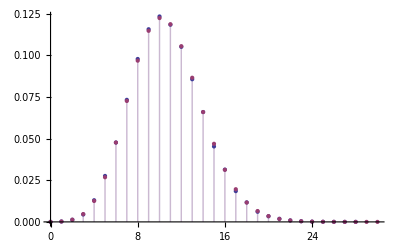

```mathematica
p1=ListPlot[{renorm@Tally[Table[npin[a,8],{100000}]],Table[{k,PDF[PoissonDistribution[8a],k]},{k,0,30}]},Filling->Axis]
```

```mathematica
getBeemDataOld[slug_,start_:0,end_:Infinity]:=Module[{s,e},
s=If[NumberQ[start]||start===Infinity,start,tm@start];
e=If[NumberQ[end]||end===Infinity,end,tm@end];
Last/@implicitZeroify@floorify[{tm@Most@#,Last@#}&/@Select[Import["http://beeminder.com/"<>slug<>".csv"],s<=tm[Most@#]<=e&]]]
```